```mathematica
(*Import["https://raw.githubusercontent.com/FeynCalc/feyncalc/master/install.m"]
InstallFeynCalc[]*)
```

Welcome to the automatic FeynCalc installer brought to you by the FeynCalc developer team!

• To install the current stable version of FeynCalc (recommended for productive use), please evaluate

InstallFeynCalc[]

• To install the development version of FeynCalc (only for experts or beta testers), please evaluate

InstallFeynCalc[InstallFeynCalcDevelopmentVersion->True]

Downloading FeynCalc from https://github.com/FeynCalc/feyncalc/archive/hotfix-stable.zip ...done! 
FeynCalc zip file was saved to C:\Users\jan-k\AppData\Local\Temp\m-2099fcac-7860-4006-b4a8-c1ceb304f99d.
Extracting FeynCalc zip file to C:\Users\jan-k\AppData\Local\Temp\m-2099fcac-7860-4006-b4a8-c1ceb304f99d.dir ...done! 
Checking the directory structure...done! 
Copying FeynCalc to C:\Users\jan-k\AppData\Roaming\Mathematica\Applications\FeynCalc ...done! 
Setting up the format type of new output cells ... done! 
Creating the configuration file ... done! 
Downloading FeynArts from https://github.com/FeynCalc/feynarts-mirror/archive/master.zip ...done! 
FeynArts zip file was saved to C:\Users\jan-k\AppData\Local\Temp\m-9917a6f2-0bb9-461b-840d-a1a04e9a0205.
Extracting FeynArts zip file to C:\Users\jan-k\AppData\Roaming\Mathematica\Applications\FeynCalc\FeynArts ...done! 
done! 
Copying FeynArts to C:\Users\jan-k\AppData\Roaming\Mathematica\Applications\FeynCalc\FeynArts ...done! 

Installation complete! Loading FeynCalc ... 
Successfully patched FeynArts.

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
description="Gl Gl -> Q Qbar, QCD, matrix element squared, tree";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
LaunchKernels[8];

$ParallelizeFeynCalc=True;
FCCheckVersion[10,2,0];
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Join::incpt: Incompatible elements in Join[<|intt→RowBox[{∫,RowBox[{■,RowBox[{ⅆ,□}]}]}],dintt→RowBox[{SubsuperscriptBox[∫,■,□],RowBox[{□,RowBox[{ⅆ,□}]}]}],rintt→RowBox[{UnderscriptBox[∫,RowBox[{■,∈,□}]],□}],sumt→RowBox[{UnderoverscriptBox[∑,RowBox[{■,=,□}],□],□}],prodt→RowBox[{UnderoverscriptBox[∏,RowBox[{■,=,□}],□],□}],«38»,cI→TemplateBox[{},CombinatorI],cK→TemplateBox[{},CombinatorK],cS→TemplateBox[{},CombinatorS],cW→TemplateBox[{},CombinatorW],cY→TemplateBox[{},CombinatorY]|>,«9»,«122»] cannot be joined.

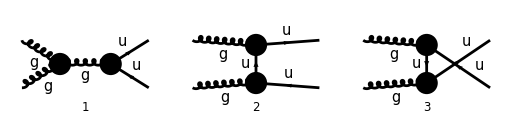

```mathematica
FCAttachTypesettingRule[p1,{SubscriptBox,p,1}]
FCAttachTypesettingRule[p2,{SubscriptBox,p,2}]
FCAttachTypesettingRule[q1,{SubscriptBox,q,1}]
FCAttachTypesettingRule[q2,{SubscriptBox,q,2}]

diags=InsertFields[CreateTopologies[0,2->2],{V[5],V[5]}->{F[3,{1}],-F[3,{1}]},InsertionLevel->{Classes},Model->"SMQCD"];

Paint[diags,ColumnsXRows->{4,1},Numbering->Simple,SheetHeader->None,ImageSize->128 {4,1}];
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},OutgoingMomenta->{q1,q2},UndoChiralSplittings->True,ChangeDimension->D,TransversePolarizationVectors->{p1,p2},List->True,SMP->True,Contract->True,DropSumOver->True];
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-q1,-q2,0,0,SMP["m_u"],SMP["m_u"]];
```

```mathematica
ampSquared[0]=SquareAmplitude[amp[0],ComplexConjugate[amp[0]],Real->True];
```

```mathematica
AbsoluteTiming[ampSquared[1]=FeynAmpDenominatorExplicit[ampSquared[0],FCParallelize->True]//SUNSimplify[#,FCParallelize->True]&;]
```

{0.137303,Null}

```mathematica
AbsoluteTiming[ampSquared[2]=ampSquared[1]//DoPolarizationSums[#,p1,p2,FCParallelize->True,ExtraFactor->1/2]&//DoPolarizationSums[#,p2,p1,FCParallelize->True,ExtraFactor->1/2]&;]
```

{0.635907,Null}

```mathematica
AbsoluteTiming[ampSquared[3]=ampSquared[2]//FermionSpinSum[#,FCParallelize->True]&//DiracSimplify[#,FCParallelize->True]&;]
AbsoluteTiming[ampSquared[4]=1/((SUNN^2-1)^2) ampSquared[3]//TrickMandelstam[#,{s,t,u,2 SMP["m_u"]^2},FCParallelize->True]&;]
```

{1.83115,Null}

{0.136549,Null}

```mathematica
ampSquared[5]=Collect2[ampSquared[4]//Total,CA,CF,D,Factoring->Function[{x},TrickMandelstam[x,{s,t,u,2 SMP["m_u"]^2}]]]
```

(D^2 C_A C_F^2 g_s^4 (-2 t m_u^2+2 m_u^4-2 u m_u^2+t^2+u^2))/(2 (1-N^2)^2 (u-m_u^2) (t-m_u^2))-(D C_A^2 C_F g_s^4 (-2 t m_u^2+2 m_u^4-2 u m_u^2+t^2+u^2))/((1-N^2)^2 s^2)-(2 D C_A C_F^2 g_s^4 (-2 t m_u^2+2 m_u^4-2 u m_u^2+t^2+u^2))/((1-N^2)^2 (u-m_u^2) (t-m_u^2))+(2 C_A^2 C_F g_s^4 (-t^3 m_u^2+2 t^2 m_u^4-3 t^2 u m_u^2-3 t u^2 m_u^2-4 t m_u^6+8 t u m_u^4-u^3 m_u^2+2 u^2 m_u^4+2 m_u^8-4 u m_u^6+2 t^3 u-2 t^2 u^2+2 t u^3))/((1-N^2)^2 s^2 (u-m_u^2) (t-m_u^2))+1/((1-N^2)^2 s^2 (u-m_u^2)^2 (t-m_u^2)^2)2 C_A C_F^2 g_s^4 (-t^5 m_u^2+7 t^4 m_u^4-11 t^4 u m_u^2-20 t^3 u^2 m_u^2-18 t^3 m_u^6+48 t^3 u m_u^4-20 t^2 u^3 m_u^2+58 t^2 u^2 m_u^4+16 t^2 m_u^8-78 t^2 u m_u^6-11 t u^4 m_u^2+48 t u^3 m_u^4-78 t u^2 m_u^6+56 t u m_u^8-u^5 m_u^2+7 u^4 m_u^4-18 u^3 m_u^6+16 u^2 m_u^8-8 m_u^12+t^5 u+6 t^3 u^3+t u^5)-(D^2 C_F g_s^4)/(2 (1-N^2)^2)+(3 D C_F g_s^4)/((1-N^2)^2)-(2 C_F g_s^4 (-2 t^3 m_u^2+9 t^2 m_u^4-18 t^2 u m_u^2-18 t u^2 m_u^2-12 t m_u^6+38 t u m_u^4-2 u^3 m_u^2+9 u^2 m_u^4-12 u m_u^6+3 t^3 u+2 t^2 u^2+3 t u^3))/((1-N^2)^2 s^2 (u-m_u^2) (t-m_u^2))

```mathematica
ampSquaredSUNN3[0]=TrickMandelstam[SUNSimplify[ampSquared[5]/. D->4,SUNNToCACF->False]/. SUNN->3,{s,t,u,0}]
```

1/(24 s^2 (u-m_u^2)^2 (t-m_u^2)^2)g_s^4 (4 s t^4 m_u^2+30 s t^3 u m_u^2-6 s t^2 u^2 m_u^2+20 s t^2 m_u^6+30 s t u^3 m_u^2+92 s t u m_u^6+4 s u^4 m_u^2+20 s u^2 m_u^6-66 s m_u^10+19 t^4 m_u^4+100 t^3 u m_u^4+68 t^2 u^2 m_u^4-27 t^2 m_u^8+100 t u^3 m_u^4+40 t u m_u^8+19 u^4 m_u^4-27 u^2 m_u^8-50 m_u^12+4 t^5 u-t^4 u^2+8 t^3 u^3-t^2 u^4+4 t u^5)